```mathematica
(*To Do
- Animate
- Create a recovery period
- Establish incubation period
```

```mathematica
TotalPop=1000;
Transfer =1;
Infectious =92;
Days=14;
InfectedA=1;
InfectedB=1;
Recovery=7;
Pops={};
PopA =Table[{k*A,RandomReal[{-Sqrt[2],Sqrt[2]}],RandomReal[{-Sqrt[2],Sqrt[2]}],"u",0},{k,1,TotalPop}];
PopB = Table[{k*B,RandomReal[{5-Sqrt[2],5+Sqrt[2]}],RandomReal[{-Sqrt[2],Sqrt[2]}],"u",0},{k,1,TotalPop}];
For[j=1,j<InfectedA+1,j++,
PopA[[j]][[4]]="i"];
For[j=1,j<InfectedB+1,j++,
PopB[[j]][[4]]="i"];

For[k=1,k<Days+1,k++,

For[i=1,i<Length[PopA]+1,i++,
If[PopA[[i]][[5]]==Recovery,
PopA[[i]][[5]]=0;
PopA[[i]][[4]]="r";]
];

For[i=1,i<Length[PopB]+1,i++,
If[PopB[[i]][[5]]==Recovery,
PopB[[i]][[5]]=0;
PopB[[i]][[4]]="r";]
];

For[i=1,i<Length[PopA]+1,i++,
If[PopA[[i]][[4]]=="i",
PopA[[i]][[5]]=PopA[[i]][[5]]+1]
];
For[i=1,i<Length[PopB]+1,i++,
If[PopB[[i]][[4]]=="i",
PopB[[i]][[5]]=PopB[[i]][[5]]+1]
];

PopA=Replace[PopA,"n"->"i",2];
PopB=Replace[PopB,"n"->"i",2];

TotalPeopleA = Length[PopA];
PeopleMetA = Random[Integer,{10,20}];
(*Print["People Met in City A"PeopleMetA];*)

TotalPeopleB = Length[PopB];
PeopleMetB = Random[Integer,{10,20}];
(*Print["People Met in City B"PeopleMetB];*)


For[j=1,j<TotalPeopleA+1, j++,
For[i=0,i<PeopleMetA,i++,
ContactA =Random[Integer,{1,TotalPeopleA}];
If[PopA[[ContactA]][[4]]=="i",
If[PopA[[j]][[4]]≠"i",
If[PopA[[j]][[4]]≠"n",
If[PopA[[j]][[4]]≠"r",
If[Random[Integer,{1,100}]> Infectious,
PopA[[j]][[4]]="n"]
]
]
],
If[PopA[[ContactA]][[4]]≠"n",
If[PopA[[ContactA]][[4]]≠"r",
If[PopA[[j]][[4]]=="i",
If[Random[Integer,{1,100}]> Infectious,
PopA[[ContactA]][[4]]="n"]
]
]
]
]
]
]
For[j=1,j<TotalPeopleB+1, j++,
For[i=0,i<PeopleMetB,i++,
ContactB =Random[Integer,{1,TotalPeopleB}];
If[PopB[[ContactB]][[4]]=="i",
If[PopB[[j]][[4]]≠"i",
If[PopB[[j]][[4]]≠"n",
If[PopB[[j]][[4]]≠"r",
If[Random[Integer,{1,100}]> Infectious,
PopB[[j]][[4]]="n"]
]
]
],
If[PopB[[ContactB]][[4]]≠"n",
If[PopB[[ContactB]][[4]]≠"r",
If[PopB[[j]][[4]]=="i",
If[Random[Integer,{1,100}]> Infectious,
PopB[[ContactB]][[4]]="n"]
]
]
]
]
]
];

ToA=RandomChoice[PopB,Transfer];
ToB=RandomChoice[PopA,Transfer];
PopA=Complement[PopA,ToB];
PopB=Complement[PopB,ToA];
For[i=1,i<Length[ToA]+1,i++,
ToA[[i]][[2]]=ToA[[i]][[2]]-5
];
For[i=1,i<Length[ToB]+1,i++,
ToB[[i]][[2]]=ToB[[i]][[2]]+5
];
PopA=Join[PopA,ToA];
PopB=Join[PopB,ToB];

Pops=Append[Pops,
Graphics[
Join[
{{Circle[{0,0},2]},{Circle[{5,0},2]}},
Table[{
If[
PopA[[i]][[4]]=="u"||PopA[[i]][[4]]=="r",
Green,
If[
PopA[[i]][[4]]=="i",
Red,Blue]
],
Circle[{PopA[[i]][[2]],PopA[[i]][[3]]},.1]},{i,1,Length[PopA]}
],
Table[{
If[
PopB[[i]][[4]]=="u"||PopB[[i]][[4]]=="r",
Green,
If[
PopB[[i]][[4]]=="i",
Red,Blue]
],
Circle[{PopB[[i]][[2]],PopB[[i]][[3]]},.1]},{i,1,Length[PopB]}
]
]
]];
]
Manipulate[
Pops[[i]],{i,1,Length[Pops],1}]
```

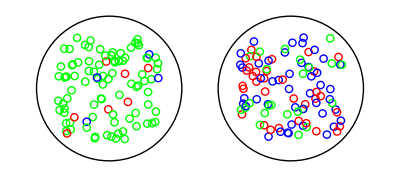

```mathematica
Print[Pops[[4]]]
```

```mathematica
PopA
```

{{4 A,-0.00938215,1.24408,r,0},{5 A,0.568205,1.34412,r,0},{7 A,-0.878031,-1.07504,r,0},{2 B,-0.297685,-0.361957,r,0},{8 B,-1.33308,-0.383311,r,0},{9 A,1.1161,-1.39975,r,0},{5 B,0.253306,0.1293,r,0},{5 B,0.253306,0.1293,r,0},{5 B,0.253306,0.1293,r,0},{5 B,0.253306,0.1293,r,0},{2 A,1.26489,1.11361,r,0},{9 A,1.1161,-1.39975,r,0},{2 A,1.26489,1.11361,r,0},{3 A,0.334518,-0.0630436,r,0},{6 B,-0.333253,1.3356,r,0}}

```mathematica
i=10
```

10

```mathematica
||PopA[[i]][[4]]=="r"||PopA[[i]][[4]]=="u"
```

True